```mathematica
eqn = x'''[t] - 2λ x''[t] - λ^2 x'[t] + 2 λ^3 x[t] == (λ^2+π^2) (2 λ Cos[π t]+π Sin[π t]);
bcs = {x[0] ==  1 + (1+ⅇ^(-2 λ)+ⅇ^-λ)/(2+ⅇ^-λ), x[1] == 0, x'[1] == (3 λ-ⅇ^-λ λ)/(2+ⅇ^-λ)};
```

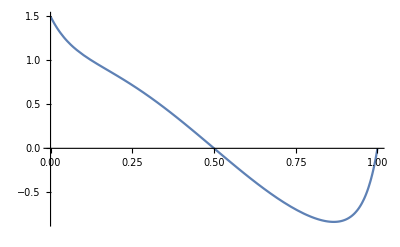

```mathematica
Block[{λ = 15}, 
sol = First[NDSolve[{eqn, bcs}, x, t, 
Method->{"Shooting", "StartingInitialConditions"->{x[2/3] == 0, x'[2/3] == 0, x''[2/3] == 0}}]];
Plot[{x[t] /. sol}, {t,0,1}]]
```

```mathematica
With[{rf=60,μ=16, Φ0=1, V0=-1,ri=0.1}, 
sol = First[NDSolve[{ψ'[r]==P[r]/r^2, P'[r]== (μ^2 r^2 Φ[r]^2)/2,Φ'[r]== F[r]/r^2, F'[r]==2 μ^2 r^2 Φ[r] ψ[r]+2 En[r] μ r^2 Φ[r], En'[r]==0, ψ[ri]== V0, F[ri]==0,Φ[ri]==Φ0, ψ[rf]== 0, Φ[rf]==0}, ψ, {r,ri,rf}, 
Method->{"Shooting", "StartingInitialConditions"->{ψ[rf]== 0, Φ[rf]==0}}]];
Plot[{ψ[r] /. sol}, {r,ri,rf}]]
```

NDSolve::ndsz: At r == 58.0788, step size is effectively zero; singularity or stiff system suspected.

ReplaceAll::reps: {ψ'[0.101224]==97.5969 P[0.101224],P'[0.101224]==1.31152 Φ[0.101224]^2,Φ'[0.101224]==97.5969 F[0.101224],F'[0.101224]==0.327879 En[0.101224] Φ[0.101224]+5.24607 Φ[0.101224] ψ[0.101224],En'[0.101224]==0,ψ[0.1]==-1,F[0.1]==0,Φ[0.1]==1,ψ[60]==0,Φ[60]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {ψ'[0.101224]==97.5969 P[0.101224],P'[0.101224]==1.31152 Φ[0.101224]^2,Φ'[0.101224]==97.5969 F[0.101224],F'[0.101224]==0.327879 En[0.101224] Φ[0.101224]+5.24607 Φ[0.101224] ψ[0.101224],En'[0.101224]==0.,ψ[0.1]==-1.,F[0.1]==0.,Φ[0.1]==1.,ψ[60.]==0.,Φ[60.]==0.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {ψ'[1.32367]==0.570741 P[1.32367],P'[1.32367]==224.27 Φ[1.32367]^2,Φ'[1.32367]==0.570741 F[1.32367],F'[1.32367]==56.0675 En[1.32367] Φ[1.32367]+897.08 Φ[1.32367] ψ[1.32367],En'[1.32367]==0,ψ[0.1]==-1,F[0.1]==0,Φ[0.1]==1,ψ[60]==0,Φ[60]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-